```mathematica
Expand[((n(n+1))/2)^2]//Expand
```

n^2/4+n^3/2+n^4/4

```mathematica
Indexed[x,1]=3
```

Set::write: Tag Indexed in Indexed[x,1] is Protected.

3

```mathematica
x[1]:=3
```

```mathematica
y[1]:=2
```

```mathematica
x[k_]:=3x[k-1]+4y[k-1]
```

```mathematica
y[k_]:=2x[k-1]+3y[k-1]
```

```mathematica
x[1]
```

3

```mathematica
x[2]
```

17

```mathematica
x[3]
```

99

```mathematica
Table[{x[k],y[k]},{k,10}]
```

{{3,2},{17,12},{99,70},{577,408},{3363,2378},{19601,13860},{114243,80782},{665857,470832},{3880899,2744210},{22619537,15994428}}

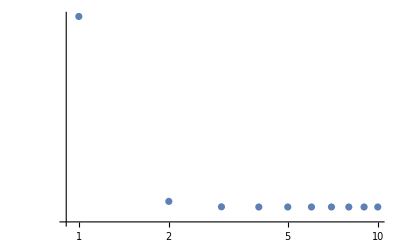

```mathematica
Table[x[k]/y[k],{k,10}]//ListLogLogPlot
```

```mathematica
Table[{k,N[x[k]/y[k]-Sqrt[2]]},{k,20}]
```

{{1,0.0857864},{2,0.0024531},{3,0.0000721519},{4,2.1239×10^-6},{5,6.25218×10^-8},{6,1.84047×10^-9},{7,5.41782×10^-11},{8,1.59472×10^-12},{9,4.68514×10^-14},{10,1.33227×10^-15},{11,0.},{12,0.},{13,0.},{14,0.},{15,0.},{16,0.},{17,0.},{18,0.},{19,0.},{20,0.}}